## Plotting Data

Hello and welcome. In previous lectures we took a look at plotting functions like Sin[x] and Exp[x]Sin[x]. Many times though, we have lists of data instead of functions and we want to be able to plot that. In today’s lecture we take a look at how to plot this kind of data.

### Range

So the first thing I’d like to look at is the Range function. The Range function basically generates lists of data.

```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

So for instance we can type:

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

This will generate the values 1 through 10. We can also generate values starting from another number.

```mathematica
Range[0,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

The third form of Range allows us to generate data in step sized of di. So for instance:

```mathematica
x=Range[0,2Pi,0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2}

In this case here, x is a variable, and we are going to use this variable later on.

### Vectorized Functions.

One of the nicest things in Mathematica is that many of the functions are vectorized. What does that mean? Let’s take a look at:

```mathematica
Sin[Pi]
```

0

Here Pi is a scalar value. The Sin function can also take a list.

```mathematica
Sin[x]
```

{0.,0.0998334,0.198669,0.29552,0.389418,0.479426,0.564642,0.644218,0.717356,0.783327,0.841471,0.891207,0.932039,0.963558,0.98545,0.997495,0.999574,0.991665,0.973848,0.9463,0.909297,0.863209,0.808496,0.745705,0.675463,0.598472,0.515501,0.42738,0.334988,0.239249,0.14112,0.0415807,-0.0583741,-0.157746,-0.255541,-0.350783,-0.44252,-0.529836,-0.611858,-0.687766,-0.756802,-0.818277,-0.871576,-0.916166,-0.951602,-0.97753,-0.993691,-0.999923,-0.996165,-0.982453,-0.958924,-0.925815,-0.883455,-0.832267,-0.772764,-0.70554,-0.631267,-0.550686,-0.464602,-0.373877,-0.279415,-0.182163,-0.0830894}

Here you can see that it evaluated Sin for each value of the list. So let’s set:

```mathematica
y=Sin[x];
```

A nice little thing in Mathematica is that you can put a semicolon at the end of your expression and it will suppress the output.

### ListPlot

So now say we wanted to plot these values. The function we use to do this is ListPlot.

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

ListPlot takes a list of y-values and plots it for us.

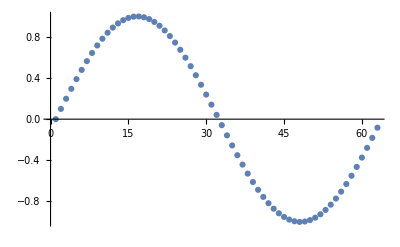

```mathematica
ListPlot[y]
```

What you’ll notice is that Mathematica will plot the Sin function, but it doesn’t have the x-values correct, and the reason for that is because it doesn’t know what the x-value should be. So it assumes that the values start from 1 and assigns them incrementally from 1 to the last value of the list. 
So if we wanted our ListPlot to be between 0 and 2π, one way that we could do that, is using the DataRange option of ListPlot.

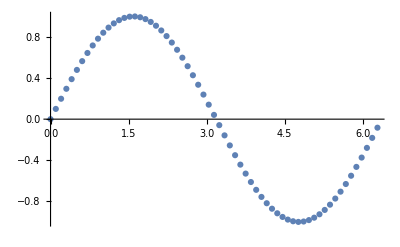

```mathematica
ListPlot[y,DataRange->{0,2Pi}]
```

### Thread

Another way that we could do this, is using the second form of ListPlot by passing a list of pairwise (x,y) values. In order to do that, we need to somehow join the x-values with y-values so that they are pairwise. We have a function in Mathematica that will do this for us.

```mathematica
?Thread
```

Thread[f[args]] "threads" f over any lists that appear in args. 
Thread[f[args],h] threads f over any objects with head h that appear in args. 
Thread[f[args],h,n] threads f over objects with head h that appear in the first n args.

So you could say:

```mathematica
Thread[{x,y}]
```

{{0.,0.},{0.1,0.0998334},{0.2,0.198669},{0.3,0.29552},{0.4,0.389418},{0.5,0.479426},{0.6,0.564642},{0.7,0.644218},{0.8,0.717356},{0.9,0.783327},{1.,0.841471},{1.1,0.891207},{1.2,0.932039},{1.3,0.963558},{1.4,0.98545},{1.5,0.997495},{1.6,0.999574},{1.7,0.991665},{1.8,0.973848},{1.9,0.9463},{2.,0.909297},{2.1,0.863209},{2.2,0.808496},{2.3,0.745705},{2.4,0.675463},{2.5,0.598472},{2.6,0.515501},{2.7,0.42738},{2.8,0.334988},{2.9,0.239249},{3.,0.14112},{3.1,0.0415807},{3.2,-0.0583741},{3.3,-0.157746},{3.4,-0.255541},{3.5,-0.350783},{3.6,-0.44252},{3.7,-0.529836},{3.8,-0.611858},{3.9,-0.687766},{4.,-0.756802},{4.1,-0.818277},{4.2,-0.871576},{4.3,-0.916166},{4.4,-0.951602},{4.5,-0.97753},{4.6,-0.993691},{4.7,-0.999923},{4.8,-0.996165},{4.9,-0.982453},{5.,-0.958924},{5.1,-0.925815},{5.2,-0.883455},{5.3,-0.832267},{5.4,-0.772764},{5.5,-0.70554},{5.6,-0.631267},{5.7,-0.550686},{5.8,-0.464602},{5.9,-0.373877},{6.,-0.279415},{6.1,-0.182163},{6.2,-0.0830894}}

Now you see that what you get back is a list of pairwise (x,y) values. We can plot this as well.

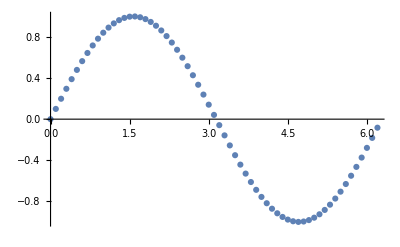

```mathematica
ListPlot[Thread[{x,y}]]
```

So now you can see that we have our ListPlot with the (x,y) values corresponding correctly.

### Table

So another way that we can get these pairwise values is using a very powerful function that you will probably end up using a lot in Mathematica. This function is Table.

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

The Table function generates lists of data. It can generate any data for which you can create an expression. For instance to generate the values 1 through 10:

```mathematica
Table[i,{i,10}]
```

{1,2,3,4,5,6,7,8,9,10}

This looks just like our Range function, but unlike the Range function, we can do a lot more here. We could say:

```mathematica
Table[i,{10}]
```

{i,i,i,i,i,i,i,i,i,i}

and now we’ll get a list of “i”. Or we could say:

```mathematica
Table["cat",{10}]
```

{cat,cat,cat,cat,cat,cat,cat,cat,cat,cat}

and get a list of “cat”.
So here we are going to generate our pairwise values of (x,y). So we’ll say:

```mathematica
Table[{i,Sin[i]},{i,0,2Pi,0.1}]
```

{{0.,0.},{0.1,0.0998334},{0.2,0.198669},{0.3,0.29552},{0.4,0.389418},{0.5,0.479426},{0.6,0.564642},{0.7,0.644218},{0.8,0.717356},{0.9,0.783327},{1.,0.841471},{1.1,0.891207},{1.2,0.932039},{1.3,0.963558},{1.4,0.98545},{1.5,0.997495},{1.6,0.999574},{1.7,0.991665},{1.8,0.973848},{1.9,0.9463},{2.,0.909297},{2.1,0.863209},{2.2,0.808496},{2.3,0.745705},{2.4,0.675463},{2.5,0.598472},{2.6,0.515501},{2.7,0.42738},{2.8,0.334988},{2.9,0.239249},{3.,0.14112},{3.1,0.0415807},{3.2,-0.0583741},{3.3,-0.157746},{3.4,-0.255541},{3.5,-0.350783},{3.6,-0.44252},{3.7,-0.529836},{3.8,-0.611858},{3.9,-0.687766},{4.,-0.756802},{4.1,-0.818277},{4.2,-0.871576},{4.3,-0.916166},{4.4,-0.951602},{4.5,-0.97753},{4.6,-0.993691},{4.7,-0.999923},{4.8,-0.996165},{4.9,-0.982453},{5.,-0.958924},{5.1,-0.925815},{5.2,-0.883455},{5.3,-0.832267},{5.4,-0.772764},{5.5,-0.70554},{5.6,-0.631267},{5.7,-0.550686},{5.8,-0.464602},{5.9,-0.373877},{6.,-0.279415},{6.1,-0.182163},{6.2,-0.0830894}}

So we have our values. Let’s see if we can ListPlot that.

```mathematica
ListPlot[Table[{i,Sin[i]},{i,0,2Pi,0.1}]]
```

-Graphics-

Awesome. So now we have our data points. Now suppose you wanted to join the data together. We can use the option Join->True.

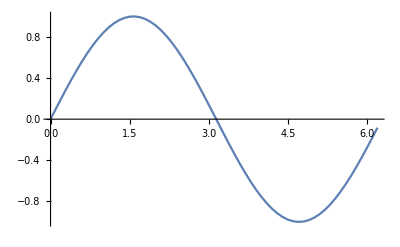

```mathematica
ListPlot[Table[{i,Sin[i]},{i,0,2Pi,0.1}],Joined->True]
```

and now we have a line.

### ListLinePlot

Another way that we can get a line plot is using the ListLinePlot function.

```mathematica
?ListLinePlot
```

System`ListLinePlot

Attributes[ListLinePlot]={Protected,ReadProtected}

```mathematica
ListLinePlot[Table[{i,Sin[i]},{i,0,2Pi,0.1}]]
```

-Graphics-

Another nice thing about functions defined in Mathematica is that the set of options to functions that do similar things, tend to be consistently named. So in previous lectures we saw how we can style our Plot. Those same options can be used here. So for instance, if we wanted to make our plot thick and black, we can do:

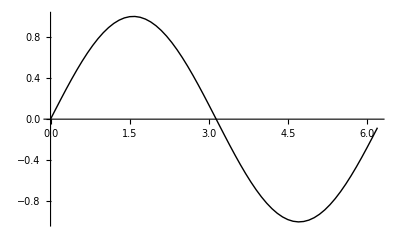

```mathematica
ListLinePlot[Table[{i,Sin[i]},{i,0,2Pi,0.1}],PlotStyle->{Thick,Black}]
```

If we wanted to make it dotted and red, we can do that as well.

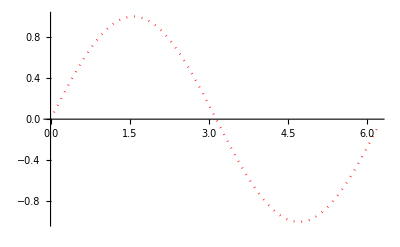

```mathematica
ListLinePlot[Table[{i,Sin[i]},{i,0,2Pi,0.1}],PlotStyle->{Dotted,Red}]
```

### Random

Now let’s take a look at an example. Imagine that you got some data from an experiment, and you expect this data to match a model. What we could do, is we could plot the data along with the function you think it should look like and visually verify they are similar. In order for us to be able to do this example, we need to generate some noisy data. So Table will come in very handy in this case. We will also use a function called Random.

```mathematica
?Random
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

Random generates a uniform pseudo distributed random number between 0 and 1. So let’s take a look at how we would generate our sine data.

```mathematica
Table[{i,Sin[i]+Random[]-0.5},{i,0,2Pi,0.1}]
```

{{0.,-0.218795},{0.1,-0.0242903},{0.2,0.490531},{0.3,0.582989},{0.4,0.229411},{0.5,0.489293},{0.6,0.256223},{0.7,0.345525},{0.8,0.919648},{0.9,0.733548},{1.,0.976669},{1.1,0.886199},{1.2,0.855063},{1.3,0.936439},{1.4,0.745989},{1.5,0.965932},{1.6,0.790157},{1.7,0.98652},{1.8,0.530146},{1.9,0.893731},{2.,0.455616},{2.1,0.658031},{2.2,0.526379},{2.3,0.475345},{2.4,0.940576},{2.5,1.01742},{2.6,0.441522},{2.7,0.369551},{2.8,0.260108},{2.9,0.148327},{3.,-0.12444},{3.1,-0.217556},{3.2,0.164454},{3.3,0.301111},{3.4,-0.156299},{3.5,-0.104912},{3.6,-0.642716},{3.7,-0.54386},{3.8,-0.773155},{3.9,-0.910332},{4.,-1.24758},{4.1,-0.327156},{4.2,-1.08917},{4.3,-0.586163},{4.4,-0.488699},{4.5,-0.781231},{4.6,-1.42917},{4.7,-0.899559},{4.8,-1.29837},{4.9,-0.705098},{5.,-0.820423},{5.1,-1.26762},{5.2,-0.610785},{5.3,-0.963991},{5.4,-0.868703},{5.5,-0.288211},{5.6,-1.08143},{5.7,-0.641266},{5.8,-0.159783},{5.9,-0.702419},{6.,-0.0293787},{6.1,0.241281},{6.2,-0.116974}}

Let’s take a look at what this plot looks like.

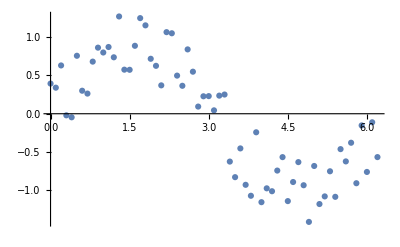

```mathematica
ListPlot[Table[{i,Sin[i]+Random[]-0.5},{i,0,2Pi,0.1}]]
```

So there is our noisy data.

### Show

In order to see our Sin function along with this ListPlot, we need to use another function in Mathematica. In previous lectures we passed lists of functions to the Plot function to see multiple plots. But in this case we have two different types of graphics objects. One is the ListPlot, and the other is the Plot function, and so we can’t pass them to the Plot function. We need to pass them to something else. This function is called Show.

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

Show basically takes a series of graphics objects and will show them on the same plot.

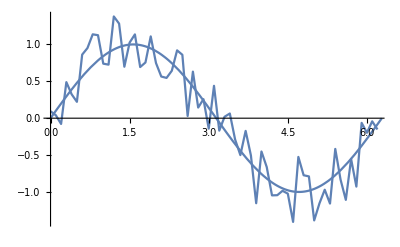

```mathematica
Show[ListPlot[Table[{i,Sin[i]+Random[]-0.5},{i,0,2Pi,0.1}],Joined->True],
Plot[Sin[x],{x,0,2Pi}]]
```

In this lecture we looked at a number of things. We demonstrated how we can generate data using the Range function as well as the Table function. We also learned how to manipulate and format data, and we showed how we can plot data. We also showed how we can plot functions overlapping with real data using the Show function. Thanks, and I hope you had fun. See you at the next lecture.